```mathematica
Psi[x_,t_,hbar_:1,mass_:1]:=Block[{alpha},alpha=hbar/(2*mass);Exp[ⅈ(x^2/(4*alpha*t)+π/4)]/(2*Sqrt[alpha*t*π])]
```

```mathematica
Manipulate[Plot[Re[Psi[x,t]],{x,-6,6}],{t,0.1,3}]
```

```mathematica
Sqrt[6]//N
```

2.44949

```mathematica
N[π,6]
```

3.14159

```mathematica
N[π,10]
```

3.141592654

```mathematica
(5+2 I)^2
```

21+20 ⅈ

```mathematica
Conjugate[Complex[5,-9]]
```

5+9 ⅈ

```mathematica
List[1,2.6,8]
```

{1,2.6,8}

```mathematica
Sin[π/4]//N
```

0.707107

```mathematica
a1 :=10*Random[]//IntegerPart
```

```mathematica
{a1,a1,a1,a1}
```

{6,7,8,3}

```mathematica
(2x+5y+6)^2/.x-> 3 /.y-> 4
```

1024

```mathematica
HoldForm[FullForm[(2x+5y+6)^2/.x-> 3 /.y-> 4]]
```

ReplaceAll[ReplaceAll[Power[Plus[Times[2,x],Times[5,y],6],2],Rule[x,3]],Rule[y,4]]

```mathematica
(a+3a)/. 4 a-> B
```

B

```mathematica
Plot3D[Sin[x]*Cos[2y],{x,-2,2},{y,-2,2},PlotTheme->"Classic"]
```

-Graphics3D-

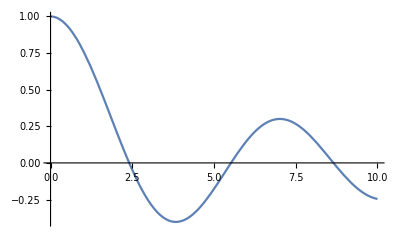

```mathematica
Plot[BesselJ[0,x],{x,0,10}]
```

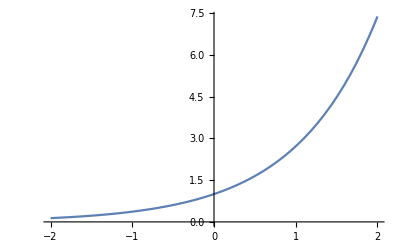

```mathematica
Plot[Exp[x],{x,-2,2}]
```

```mathematica
Solve[x^3-2 x^2+3x-2==0,x]
```

{{x→1},{x→1/2 (1-ⅈ √7)},{x→1/2 (1+ⅈ √7)}}

```mathematica
Solve[{2x-4y==3,x+5y==-2},{x,y}]
```

{{x→1/2,y→-1/2}}

```mathematica
NSolve[{2x-4y==3,x+5y==-2},{x,y}]
```

{{x→0.5,y→-0.5}}

```mathematica
NSolve[{2 x^2-y==1,x+y^2==2},{x,y}]
```

{{x→1.,y→1.},{x→0.089826-0.451507 ⅈ,y→-1.39158-0.162228 ⅈ},{x→0.089826+0.451507 ⅈ,y→-1.39158+0.162228 ⅈ},{x→-1.17965,y→1.78316}}

```mathematica
f[x_]:=x^3+2Cos[x]
```

```mathematica
{f'[x],f''[x]}
```

{3 x^2-2 sin(x),6 x-2 cos(x)}

```mathematica
(f^4)[x]
```

f^4(x)

```mathematica
Integrate[f[x],x]
```

x^4/4+2 sin(x)

```mathematica
Integrate[Tan[Sin[x]],{x,0,π}]
```

∫_0^π tan(sin(x))ⅆx

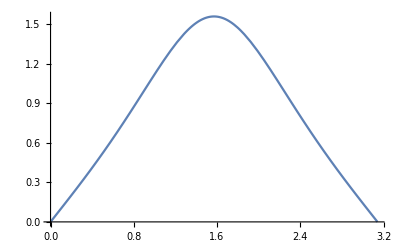

```mathematica
Plot[Tan[Sin[x]],{x,0,π}]
```

```mathematica
NIntegrate[Tan[Sin[x]],{x,0,π}]
```

2.66428

```mathematica
Sum[n,{n,1,n}]
```

1/2 n (n+1)

```mathematica
Sum[n,{n,1,n}]
```

1/2 n (n+1)

```mathematica
data = Table[{x,Cos[x]+0.25*Random[]},{x,0,2*π,0.2}];
```

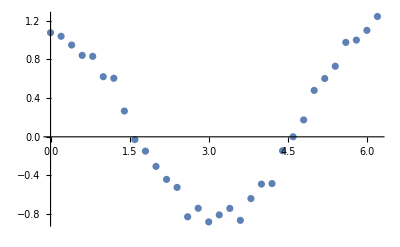

```mathematica
pl = ListPlot[data]
```

```mathematica
s = Fit[data,{1,x,x^2},x]
```

0.222588 x^2-1.37803 x+1.51413

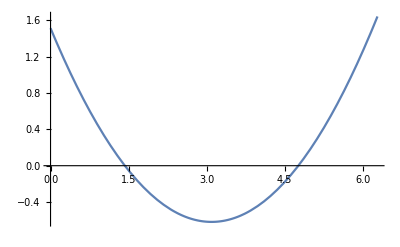

```mathematica
pls = Plot[datafit,{x,0,2π},DisplayFunction->Identity]
```

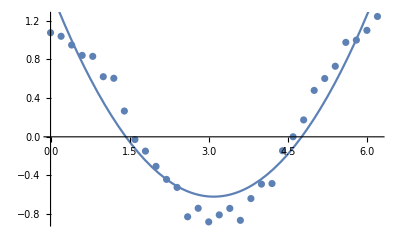

```mathematica
Show[pl,pls,DisplayFunction-> $DisplayFunction]
```

```mathematica
x = π/4; u:=Sin[x]+Cos[y]^2;
```

```mathematica
Block[{x=π/2,y=π/4},u+1]
```

5/2

```mathematica
u
```

cos^2(y)+1/(√2)

```mathematica
Module[{x=π/2,y=π/4},u+1]
```

cos^2(y)+1/(√2)+1